## Import Data

Use a local copy of the data provided by Christelle Ekosso on 06 July 2023, via Slack.

```mathematica
SeedRandom[1841]; (*set a random seed for training/test set generation for replicability*)
SetDirectory@NotebookDirectory[];
<<"src/platereader.wl"
```

```mathematica
Short[spectra=importPlateReaderFile["data/Universal Indicatory Array.txt"]]

measuredpH = Import[
"data/Copy of Universal Indicatory Array.xlsx",
{"Data",2,3;;40,4},
"EmptyField"->Nothing ]
```

{350→{0.71075,0.67575,0.10975,0.17575,0.13475,0.21875,«84»,-0.03625,-0.03525,-0.03325,-0.02325,-0.03225,-0.03325},«40»}

{4.75,4.72,4.87,5.28,5.5,5.8,6.14,6.81,7.3,7.55,7.8,8.03,8.12,8.27,8.33,8.7,8.77,9.21,9.11,9.41,10.61,10.27,11.66,11.44,11.23,11.72,11.92,12.16,12.17,11.9,12.15,12.2,12.21,12.32,12.16,11.94}

```mathematica
createDataset[spectra_List,pH_List]:=Table[ (spectra[[All,2,i]]->pH[[i]]), {i, Length[pH]}]

data=createDataset[spectra,measuredpH];
wavelengths=spectra[[All,1]];
```

### Visualize a sample

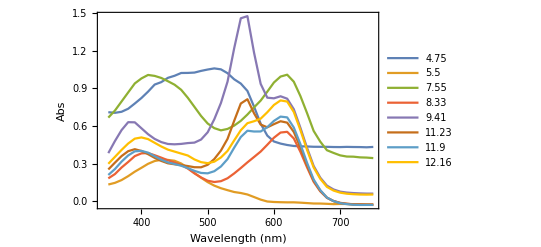

```mathematica
ListLinePlot[
{data[[1]],data[[5]],data[[10]],data[[15]],data[[20]],data[[25]],data[[30]],data[[35]]},
PlotLegends->data[[{1,5,10,15,20,25,30,35},2]],
DataRange->MinMax[wavelengths],
Frame->True,
FrameLabel->{"Wavelength (nm)","Abs"}
]
```

Comment:  It doesn’t appear that there is a consistent baseline (“zero”) for these spectra, which might cause problems later.  Let’s take a look at the first 3 spectra, which are pretty close in pH and illustrates the “wandering baseline” problem:

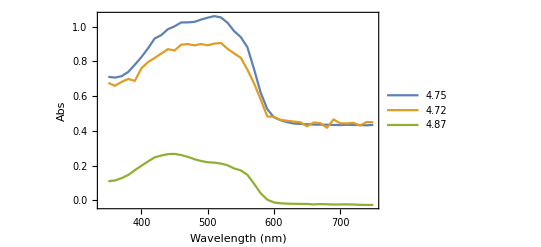

```mathematica
ListLinePlot[
{data[[1]],data[[2]],data[[3]]},
PlotLegends->data[[{1,2,3},2]],
DataRange->MinMax[wavelengths],
Frame->True,
FrameLabel->{"Wavelength (nm)","Abs"}
]
```

Comment:  It may be valuable to normalize the spectra in some way; this will be essential for the earthmover distance calculation.  We will revisit this below.

### Visualize the blanks

The last row of wells in the 96-well SBS plate are a water blank, as described on Sheet 2 of the spreadsheet.

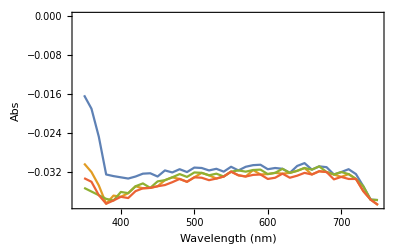

```mathematica
ListLinePlot[
{spectra[[All,2,-12]],spectra[[All,2,-9]],spectra[[All,2,-5]],spectra[[All,2,-1]]},
DataRange->MinMax[wavelengths],
Frame->True,
FrameLabel->{"Wavelength (nm)","Abs"},
PlotRange->All]
```

## Approach 1: Principal Components Analysis

Perform principal components analysis to reduce the dimensionality of the problem, then use either linear regression or a nearest-neighbor model to assign the pH.

```mathematica
pca=DimensionReduction[data[[All,1]],Method->"PrincipalComponentsAnalysis"]
transformedData=Table[(pca[entry[[1]]]->entry[[2]]), {entry, data}];
```

DimensionReducerFunction[…]

Define a convenience function for cross validating different model types:

```mathematica
crossValidate[data_,modelType_String]:=ResourceFunction["CrossValidateModel"][
data,
Predict[#,Method->modelType]&,
"ValidationFunction"->{Automatic,{"MeanDeviation","RSquared"}}
]
```

```mathematica
(*Mean absolute error and R^2, over 5-fold cross validation*)
cvLinearRegressionSummary=crossValidate[transformedData,"LinearRegression"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{1.080.11,0.670.11}

```mathematica
cvNearestNeighborSummary=crossValidate[transformedData,"NearestNeighbors"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{1.390.16,0.500.07}

```mathematica
cvRFSummary=crossValidate[transformedData,"RandomForest"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{1.370.16,0.560.05}

```mathematica
cvGBTSummary=crossValidate[transformedData,"GradientBoostedTrees"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{1.290.31,0.530.16}

Conclusion:  Reducing the dimensionality to 2 dimensions (by PCA) allows for a linear regression model to predict pH with a mean error of 1 pH unit, from the spectroscopic observation, as established by 5-fold cross validation (based on training the model on ~28 examples and evaluating on ~7 test cases); other models are worse.

## How good can a nearest-neighbor model perform with this dataset

For reference:  If the error was bounded by the distance to the nearest example...how much would our pH error be? (In other words, if we had a perfect classifier that had to put things into the nearest example, how close would it be? Assess this by sampling 5 times

```mathematica
sample=Table[
{train,test}=ResourceFunction["TrainTestSplit"][measuredpH];
pred=Flatten[ First/@Nearest[train]/@test];
{Mean@Abs[test-pred],Correlation[test,pred]^2},
{i,5}];
MeanAround/@Transpose[sample]
```

{0.1480.019,0.99400.0017}

## Approach 2: Optimal Transport Classifier

Concept:  Try to find the most similar spectrum (by Earth Mover Distance, aka W1 Wasserstein metric) and assign that pH to the unknown spectrum.

Further reading:
See:  https://en.wikipedia.org/wiki/Earth_mover%27s_distance
See: JCP 2021 https://doi.org/10.1063/5.0069681
See: JCP 2022 https://doi.org/10.1063/5.0087385

### Data processing

We need the spectra to be positive and sum to 1; shift by the smallest value (using a scalar addition) and then normalize by the Total value of the vector:

```mathematica
normalizeSpectrum[l_?VectorQ]:=Normalize[#,Total]&@(l-Min[l])

normalizedData=Table[(normalizeSpectrum[entry[[1]]]->entry[[2]]), {entry, data}];
```

This seems to improve the wandering baseline issue noted above:

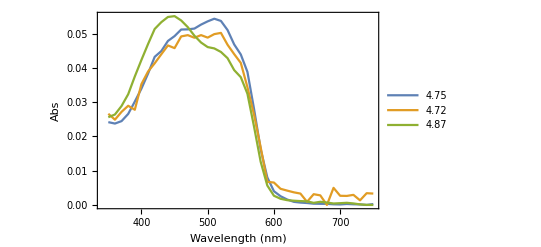

```mathematica
ListLinePlot[
{normalizedData[[1]], normalizedData[[2]], normalizedData[[3]]},
PlotLegends->data[[{1,2,3},2]],
DataRange->MinMax[wavelengths],
Frame->True,
FrameLabel->{"Wavelength (nm)","Abs"},
PlotRange->All
]
```

### Model construction and analysis

```mathematica
<<"src/emd.wl" (*import the earth mover distance code*)
```

```mathematica
(* define a function for model validation during CV, as EMD is not a built-in classifier *)
validation[model_NearestFunction,validationData_List]:=With[
{obs=validationData[[All,2]],
predicted = model/@validationData[[All,1]]//Flatten},
{Mean@Abs[obs-predicted], Correlation[obs,predicted]^2}]

(* perform 5-fold cross validation of the EMD model *)
cvEMDSummary=ResourceFunction["CrossValidateModel"][
normalizedData,
Nearest[#,DistanceFunction->emd]&, (*model definition*)
"ValidationFunction"->validation];

(* collect summary statistics *)
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{0.410.08,0.9380.026}

Comment:  Observe how the pH error is less than half of what we observed previously; still about 3x the theoretical minimum.

### Aside: What do the normalized spectra look like over a range of pH values?

Make the same plot we generated at the beginning, but now using the normalized values.

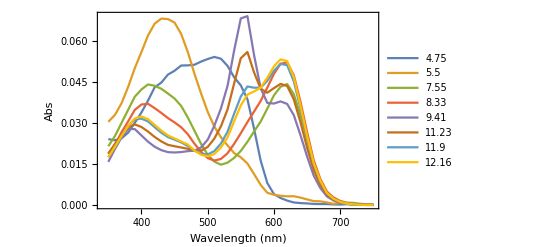

```mathematica
ListLinePlot[
{normalizedData[[1]],normalizedData[[5]],normalizedData[[10]],normalizedData[[15]],normalizedData[[20]],normalizedData[[25]],normalizedData[[30]],normalizedData[[35]]},
PlotLegends->data[[{1,5,10,15,20,25,30,35},2]],
DataRange->MinMax[wavelengths],
Frame->True,
FrameLabel->{"Wavelength (nm)","Abs"}
]
```

### Aside: How well would our old classifiers work if we use the normalized data instead?

We had noted earlier that the spectra did not appear to have a consistent baseline.  What happens if we use the normalization described above?

```mathematica
crossValidate[normalizedData,"LinearRegression"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{0.600.13,0.850.08}

```mathematica
crossValidate[normalizedData,"NearestNeighbors"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{0.580.08,0.760.09}

Comment: This appears to improve the models, and the model are now getting closer to the optimal transport value)

### Aside: What if we PCA transform the normalized data and then use a standard regression model?

What if we use this normalized data as the input to PCA?

```mathematica
pca2=DimensionReduction[normalizedData[[All,1]],Method->"PrincipalComponentsAnalysis"]
pca2Data=Table[(pca2[entry[[1]]]->entry[[2]]), {entry, normalizedData}];
```

DimensionReducerFunction[…]

Re-run the model generation and cross validation:

```mathematica
crossValidate[pca2Data,"LinearRegression"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]

crossValidate[pca2Data,"NearestNeighbors"];
MeanAround/@Transpose@%[[All,"ValidationResult"]]
```

{1.450.09,0.440.19}

{0.570.12,0.850.07}

Comment:  This slightly (probably not meaningfully) improves the nearest neighbor metric, but makes the linear model worse; we could play around with other dimensional embeddings if desired, but this does not seem promising.

## Discussion items and next steps

Discuss proper approach to blanking and normalization.

Is +/-0.5 pH units good enough?  If so, then I recommend proceeding with the earthmover distance based metric

It would be useful to acquire another batch of data (perhaps even the “same” experiments) to be able to assess variations between different experiment conditions (running on a different day, different plate, etc.)

My understanding is that these are still very “clean” systems; we may wish to try adding impurities to see the extent to which they screw up the spectra.

What’s the right way to deploy this for the intended science goals?